## Import

```mathematica
mldir="/home/jwb/repos/github-research/csvs/Individuals/Pretty/ML/";
stackdir = "/home/jwb/repos/github-research/csvs/Individuals/Pretty/Stack/";
exportdir="/home/jwb/repos/github-research/MLMetrics/Frequency Analysis/";
newdir = "/home/jwb/repos/github-research/MLMetrics/Committers/csvs/";
```

```mathematica
data`raw=Import["/home/jwb/repos/github-research/csvs/Individuals/Pretty/ML/torch7-torch-commits.csv","Data"];
```

```mathematica
data`bigML=Import[#,"Data"]&/@Cases[FileNames["*.csv",mldir],x_/;!StringContainsQ[x,"ystem"]];
data`bigStack=Import[#,"Data"]&/@FileNames["*.csv",stackdir];
data`bigNew = Import[#,"Data"]&/@Cases[FileNames["*.csv",newdir],x_/;!StringContainsQ[x,"ystem"]];
mlLabels={"Caffe","CNTK","DL4J","TensorFlow","Theano","Torch7"};
stackLabels={"Cinder","Cloudstack","Glance","Horizon","Keystone","Neutron","Nova","Swift"};
```

```mathematica
Dimensions[data`bigNew]
```

{6}

## Functions

```mathematica
hist[set_,labels_,dir_]:=Table[Export[exportdir<>"Histograms/"<>dir<>labels[[n]]<>"Histogram.png",Histogram[Map[Total,set[[n]][[2;;]][[All,2;;]]],AxesLabel->{"People","Commits"},PlotLabel->labels[[n]],ImageSize->Large,LabelStyle->Directive[Bold]]],{n,Length@labels}];
```

```mathematica
fftShift[n_]:=Abs[Fourier[n]][[;;(Floor@(Length[n]/2))]]

fftPlot[n_]:=Rasterize@ListLinePlot[fftShift[n],PlotRange->Full,ImageSize->Large]

avgFFT[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
Mean@fft
]
avgFFTr[n_]:=Module[{tail,fft},
tail=Cases[n[[2;;]][[All,2;;]],x_/;Total[x]≠1];
fft=fftShift/@tail;
Mean@fft
]
avgFFTgeo[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
GeometricMean@fft
]

avgFFTnorm[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
(Mean@fft)/Total[tail,2]
]
avgFFTnormr[n_]:=Module[{tail,fft},
tail=Cases[n[[2;;]][[All,2;;]],x_/;Total[x]≠1];
fft=fftShift/@tail;
(Mean@fft)/Total[tail,2]
]
avgFFTgeonorm[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
(GeometricMean@fft)/Total[tail,2]
]

fftVis[n_,labels_]:=Rasterize@ListLinePlot[n,PlotRange->Full,ImageSize->Large, PlotLegends->labels]
```

## Example Single Repository

```mathematica
data`tail=data`raw[[2;;]][[All,2;;]];
data`fft=fftShift/@data`tail;
data`avgfft=Mean@data`fft;
fftVis[data`avgfft,mlLabels]
```

-Graphics-

```mathematica
fftVis[(data`avgfft)/Log[Total[data`tail,2]]]
```

-Graphics-

## Analysis

### Unnormalized Frequency Analysis

#### ML

```mathematica
fftVis[avgFFTr/@data`bigML,mlLabels]
Export[exportdir<>"UnnormalizedFilteredML.png",%];
```

-Graphics-

#### Stack

```mathematica
fftVis[avgFFTr/@data`bigStack,stackLabels]
Export[exportdir<>"UnnormalizedFilteredStack.png",%];
```

-Graphics-

### Normalized Analysis by Commits

#### ML

```mathematica
fftVis[avgFFTnormr/@data`bigML,mlLabels]
Export[exportdir<>"NormalizedFilteredML.png",%];
```

-Graphics-

#### Stack

```mathematica
fftVis[avgFFTnormr/@data`bigStack,stackLabels]
Export[exportdir<>"NormalizedFilteredStack.png",%];
```

-Graphics-

## Histogram Function

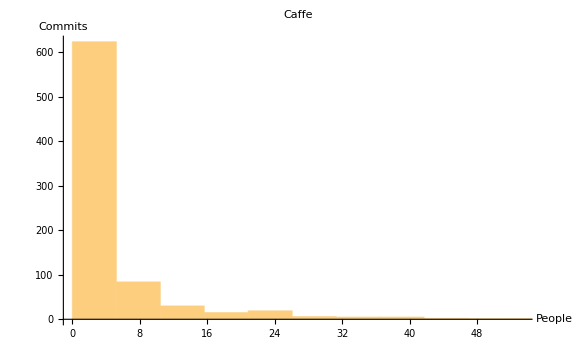
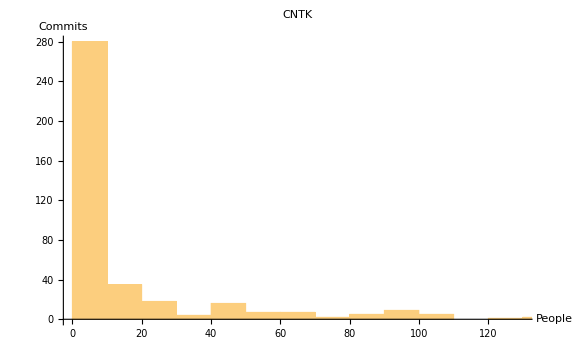
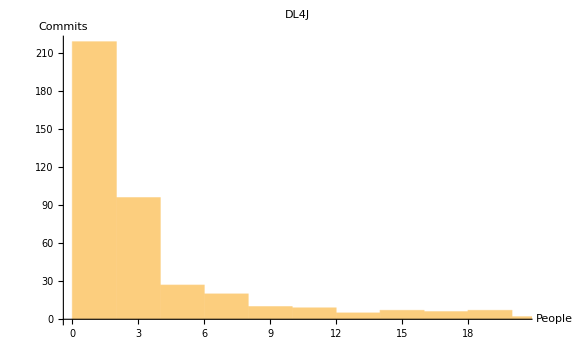
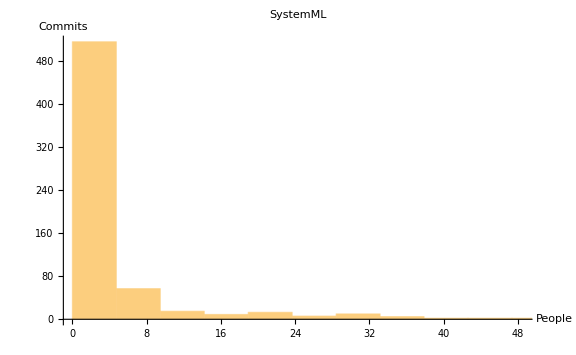
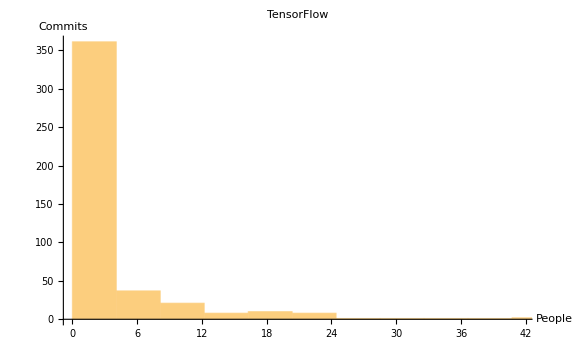
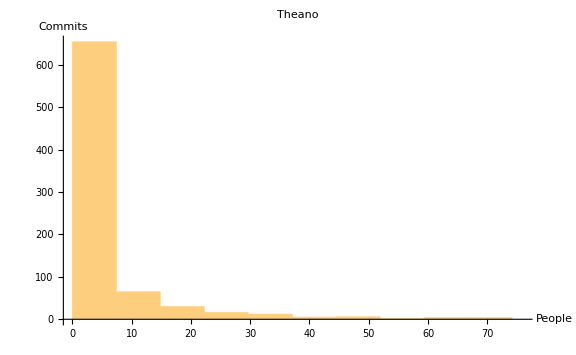
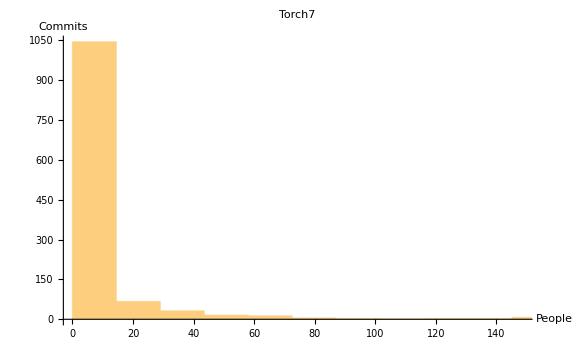

```mathematica
Table[Histogram[Map[Total,data`bigStack[[n]][[2;;]][[All,2;;]]],AxesLabel->{"People","Commits"},PlotLabel->mlLabels[[n]],ImageSize->Large,LabelStyle->Directive[Bold]],{n,Length@mlLabels}]
```

```mathematica
hist[data`bigML,mlLabels,"ML/"];
```

```mathematica
Table[Export[exportdir<>"Histograms/LongForm/"<>"ML/"<>mlLabels[[n]]<>"LogLogHistogram.png",
ListLogLogPlot[
Sort[
Map[
Total,data`bigML[[n]][[2;;]][[All,2;;]
]
],Greater
],PlotRange->Full,PlotLabel->mlLabels[[n]],AxesLabel->{"Contributor Rank","Number of Commits"},PlotStyle->colorMap,ImageSize->Large,Joined->True]
]
,{n,Length@mlLabels}];
```

```mathematica
Export[exportdir<>"Histograms/LongForm/ML/FullNormalizedHistogram.png",ListLogPlot[Table[
Sort[
Map[
Total,data`bigML[[n]][[2;;]][[All,2;;]
]
],Greater
],{n,Length@mlLabels}],PlotRange->Full,PlotLegends->mlLabels,AxesLabel->{"Contributor Rank","Number of Commits"},PlotStyle->colorMap,ImageSize->Large,Joined->True,DataRange->{1,1000}]]
```

/home/jwb/repos/github-research/MLMetrics/Frequency Analysis/Histograms/LongForm/ML/FullNormalizedHistogram.png

```mathematica
colorMap={"Purple","Brown","Green","Yellow","Blue","Red"};
```

## New

```mathematica
data`bigNew[[1]][[All,2]]
```

{1,1,5,1,2,17,1,1,1,1,1,1,1,1,1,1,5,1,5,2,1,3,1,1,42,1,16,1,3,5,1,27,1,1,1,5,145,6,1,2,1,2,1,3,2,1,1,4,2,2,23,1,1,1,1,1,1,1,1,1,1,3,1,1,2,2,1,2,1,1,1,1,793,1,1,1,8,2,6,1,82,1,7,1,1,7,4,1,1,10,1,2,1,1,1,8,1,2,1,3,1,6,1,1,1,1,1,1,2,1,1,9,1,1,1,10,1,3,1,23,2,9,1,4,1,1,1,2,2,5,2,117,1,1,2,2,1,1,2,1,6,1,7,1,3,16,78,5,3,2,7,2,1,1,1,2,1,1,1,3,1,1,3,6,2,1,1,1,1,12,2,2,3,4,17,1,2,1,1,1,1,2,2,6,2,1,1,4,1,1,2,3,1016,1,1,10,1,1,2,1,79,2,1,2,1,1,7,1,1,3,12,1,1,1,21,2,1,1,2,39,3,3,409,1,1,2,1,2,8,2,1,12,1,90,1,1,1,1,1,2,2,1,262,1,1,1,11,1,1,1}

```mathematica
Export[exportdir<>"Histograms/New/LogLogFull.png",ListLogLogPlot[Table[
Sort[
data`bigNew[[n]][[All,2]]
,Greater
],{n,Length@mlLabels}],PlotRange->Full,PlotLegends->mlLabels,AxesLabel->{"Contributor Rank","Number of Commits"},PlotStyle->colorMap,ImageSize->Full,Joined->True]]
```

/home/jwb/repos/github-research/MLMetrics/Frequency Analysis/Histograms/New/LogLogFull.png